# Testing the Amplitude for 1 to 1

```mathematica
rmin=-3;
rmax=3;
```

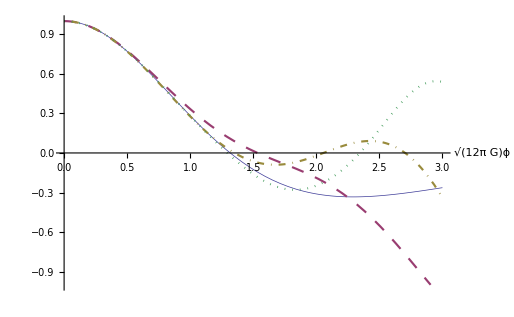

```mathematica
ptot = Plot[{Re[aex],Re[atot2],Re[atot4],Re[atot6]},{x,0,3},AxesLabel->{"√(12π G)ϕ",},PlotRange->{-1,1},LabelStyle->Medium,PlotStyle->{{Thickness[0.001]}, {Thickness[0.003],Dashing[{Medium}]},{Thickness[0.003],DotDashed},{Thickness[0.003],Dotted}}]
```

## Exact Result

```mathematica
aex = Aexact[1,1];
```

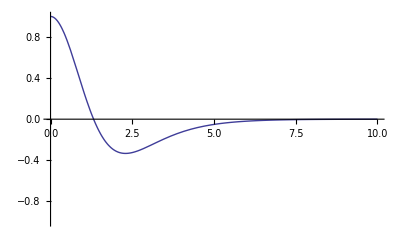

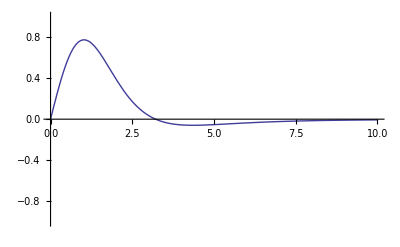

```mathematica
prex=Plot[Re[aex],{x,0,10},PlotRange->{-1,1}]
piex=Plot[Im[aex],{x,0,10},PlotRange->{-1,1}]
```

## Zeroth order paths:

```mathematica
Amp0[v_]:=Amplitude[{v}];
a0=Amp0[1]
```

ⅇ^(1.2605 ⅈ x)

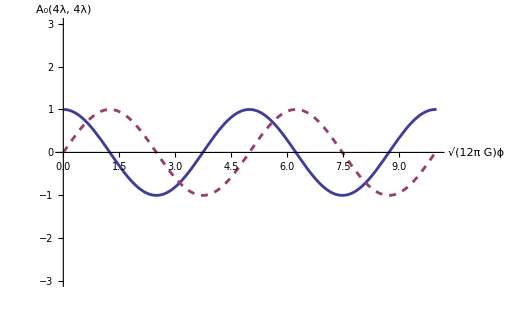

```mathematica
pre0 = Plot[{Re[a0],Im[a0]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_0(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

## Second Order Paths :

```mathematica
Generate2[2,10];
ManyChange[basetot];
a2=ManyC;
```

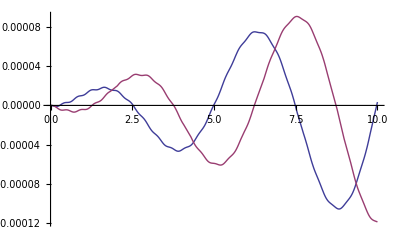

```mathematica
Generate3[2,11];
ManyChange[basetot];
a211=ManyC;
Plot[{Re[a211],Im[a211]},{x,0,10}]
```

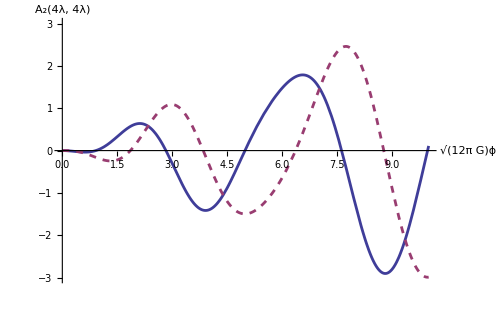

```mathematica
pre2 = Plot[{Re[a2],Im[a2]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_2(4λ, 4λ)"},PlotRange->{rmin,rmax},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

```mathematica
atot2=a2+a0;
```

## Third Order Paths :

```mathematica
Generate2[3,6];
ManyChange[basetot];
a30=ManyC;
```

```mathematica
Generate3[3,7];
ManyChange[basetot];
a37=ManyC;
```

```mathematica
Generate3[3,8];
ManyChange[basetot];
a38=ManyC;
```

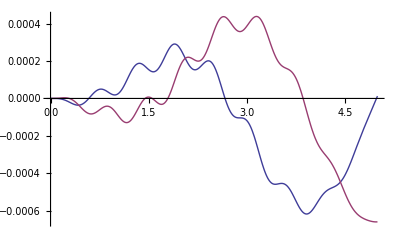

```mathematica
Plot[{Re[a38],Im[a38]},{x,0,5}]
```

```mathematica
a3=a30+a37+a38;
```

```mathematica
atot3=a0+a2+a3;
```

## Fourth Order Paths

```mathematica
Generate3[4,2];
ManyChange[basetot];
a42=ManyC;
```

```mathematica
Generate3[4,3];
ManyChange[basetot];
a43=ManyC;
```

```mathematica
Generate3[4,4];
ManyChange[basetot];
a44=ManyC;
```

```mathematica
Generate3[4,5];
ManyChange[basetot];
a45=ManyC;
```

```mathematica
Generate3[4,6];
ManyChange[basetot];
a46=ManyC;
```

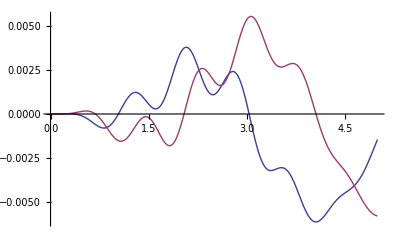

```mathematica
Plot[{Re[a46],Im[a46]},{x,0,5}]
```

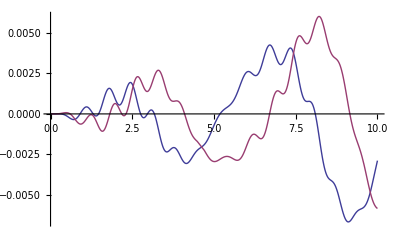

```mathematica
Generate3[4,7];
ManyChange[basetot];
a47=ManyC;
Plot[{Re[a47],Im[a47]},{x,0,10}]
```

```mathematica
a4=a42+a43+a44+a45+a46;
```

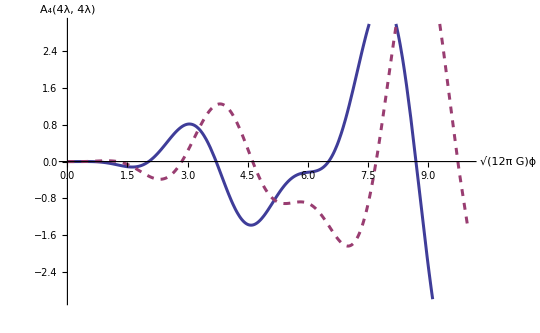

```mathematica
pre4 = Plot[{Re[a4],Im[a4]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_4(4λ, 4λ)"},PlotRange->{-3,3},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

```mathematica
atot4=a0+a2+a3+a4;
```

## Fifth Order

```mathematica
Generate3[5,3];
ManyChange[basetot];
a53=ManyC;
```

```mathematica
Generate3[5,4];
ManyChange[basetot];
a54=ManyC;
```

```mathematica
Generate3[5,5];
ManyChange[basetot];
a55=ManyC;
```

```mathematica
Generate3[5,6];
ManyChange[basetot];
a56=ManyC;
```

```mathematica
Generate3[5,7];
ManyChange[basetot];
a57=ManyC;
```

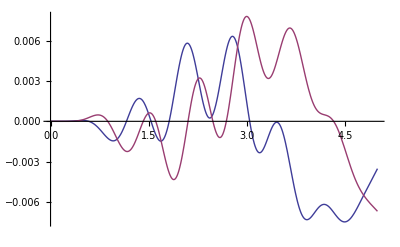

```mathematica
Plot[{Re[a57],Im[a57]},{x,0,5}]
```

```mathematica
a5=a53+a54+a55+a56+a57;
```

```mathematica
atot5=a0+a2+a3+a4+a5;
```

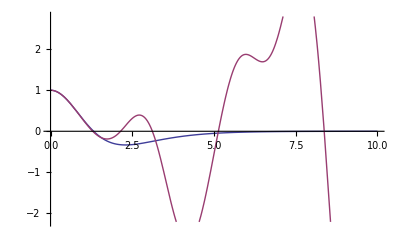

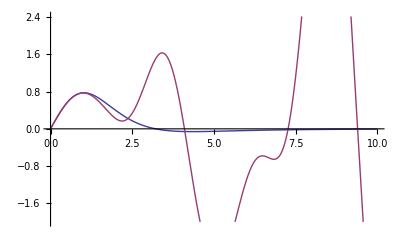

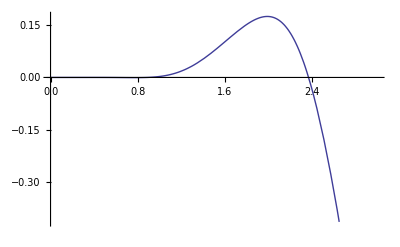

```mathematica
ptre5 = Plot[{Re[aex],Re[atot5]},{x,0,10}]
ptim5 = Plot[{Im[aex],Im[atot5]},{x,0,10}]
Plot[Im[aex-atot5],{x,0,3}]
```

## Sixth Order

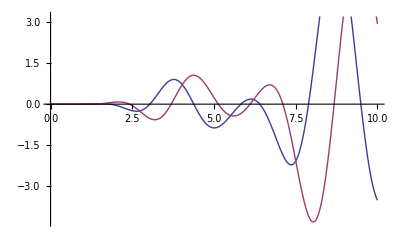

```mathematica
Generate3[6,3];
ManyChange[basetot];
a63=ManyC;
Plot[{Re[a63],Im[a63]},{x,0,10}]
```

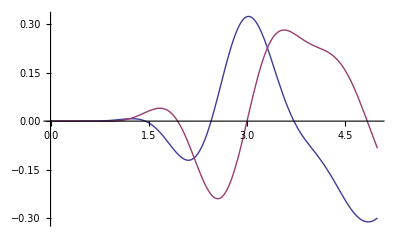

```mathematica
Generate3[6,4];
ManyChange[basetot];
a64=ManyC;
Plot[{Re[a64],Im[a64]},{x,0,5}]
```

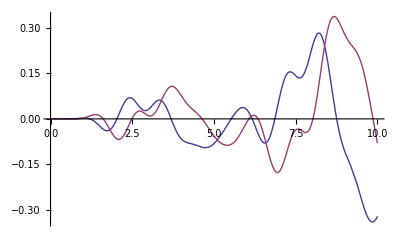

```mathematica
Generate3[6,5];
ManyChange[basetot];
a65=ManyC;
Plot[{Re[a65],Im[a65]},{x,0,5}]
```

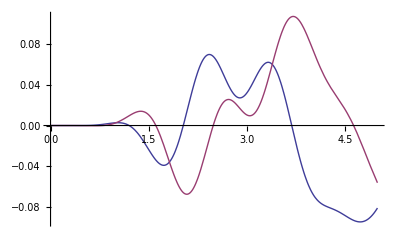

```mathematica
Generate3[6,6];
ManyChange[basetot];
a66=ManyC;
Plot[{Re[a65],Im[a65]},{x,0,5}]
```

```mathematica
a6=a63+a64+a65+a66;
```

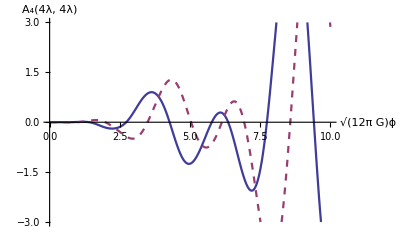

```mathematica
pre6 = Plot[{Re[a6],Im[a6]},{x,0,10},AxesLabel->{"√(12π G)ϕ","A_4(4λ, 4λ)"},PlotRange->{-3,3},LabelStyle->Medium,PlotStyle->{Thickness[0.004], {Thickness[0.004],Dashed}}]
```

```mathematica
atot6=a0+a2+a3+a4+a5+a6;
```